```mathematica
data=Import["/home/ubu/Downloads/Vereinsliste.csv",CharacterEncoding->"UTF8"];
```

```mathematica
rang=Import["/home/ubu/Downloads/tabu15.csv",CharacterEncoding->"UTF8"];
```

```mathematica
rang2=Import["/home/ubu/Downloads/tabneu.csv",CharacterEncoding->"UTF8"];
```

```mathematica
rang3=Import["/home/ubu/Downloads/tabneu2.csv",CharacterEncoding->"UTF8"];
```

```mathematica
rang4=Import["/home/ubu/Downloads/tabprofis2.csv",CharacterEncoding->"UTF8"];
```

```mathematica
?StringMatchQ
```

StringMatchQ[string,patt] tests whether "string" matches the string pattern patt. 
StringMatchQ[string,RegularExpression[regex]] tests whether "string" matches the specified regular expression. 
StringMatchQ[{s_1,s_2,…},p] gives the list of results for each of the s_i.

```mathematica
data[[2,3]]
```

10

```mathematica
data[[2,1]]
```

FC Bayern München

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
bayern=Select[data,#[[1]]==="FC Bayern München"&];
```

```mathematica
bayernU15=Select[bayern,#[[2]]==="U15"&];
```

```mathematica
bayernU15geb=bayernU15[[All,3]]
```

{10,21,45,45,48,49,62,67,92,95,109,165,166,168,217,218,237,262}

```mathematica
Median[bayernU15[[All,3]]]
```

187/2

```mathematica
%//N
```

93.5

```mathematica
nuernberg=Select[data,#[[1]]==="1. FC Nürnberg"&];
```

```mathematica
Median[nuernberg[[All,3]]]
```

84

```mathematica
gladbach=Select[data,#[[1]]==="Borussia Mönchengladbach"&];
```

```mathematica
gladbachprofis=Select[gladbach,#[[2]]==="Profis"&];
```

```mathematica
KolmogorovSmirnovTest[gladbachprofis[[All,3]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

0.0145548

```mathematica
Median[gladbachprofis[[All,3]]]
```

285/2

```mathematica
%//N
```

142.5

```mathematica
gladbachprofis[[All,3]]
```

{8,15,35,43,49,80,83,97,112,120,122,132,137,148,151,152,167,167,169,172,213,291,297,304,309,332}

```mathematica
bayernprofis=Select[bayern,#[[2]]==="Profis"&];
```

```mathematica
KolmogorovSmirnovTest[bayernprofis[[All,3]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

0.764616

```mathematica
Median[bayernprofis[[All,3]]]
```

183

```mathematica
KolmogorovSmirnovTest[bayernU15geb,UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

0.0396433

```mathematica
ListLinePlot[bayernU15[[All,7]]]
```

```mathematica
Length[bayernU15[[All,7]]]
```

22

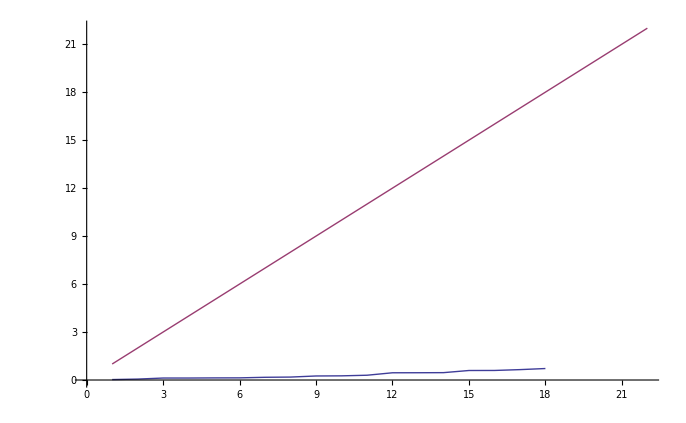

```mathematica
ListLinePlot[{Sort[1/365*bayernU15[[All,3]]],Range[22]}]
```

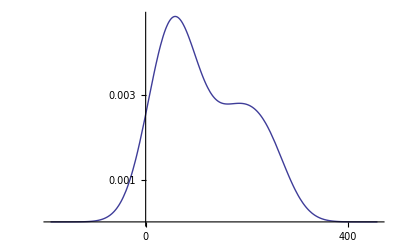

```mathematica
SmoothHistogram[bayernU15geb]
```

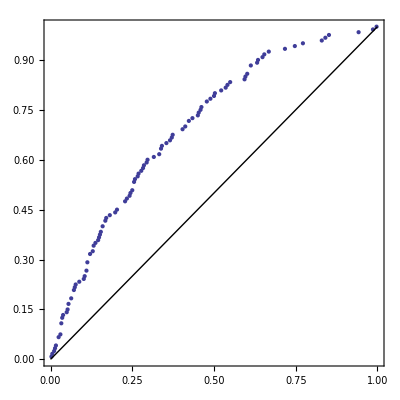

```mathematica
ProbabilityPlot[alleU15[[All,3]],UniformDistribution[{1,365}]]
```

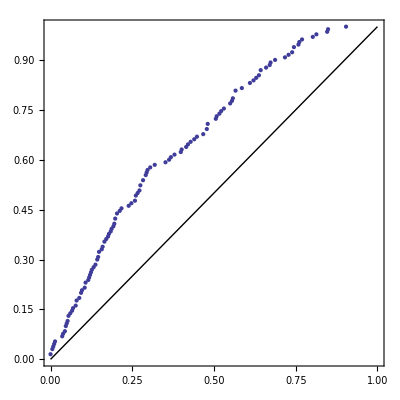

```mathematica
ProbabilityPlot[alleU17[[All,3]],UniformDistribution[{1,365}]]
```

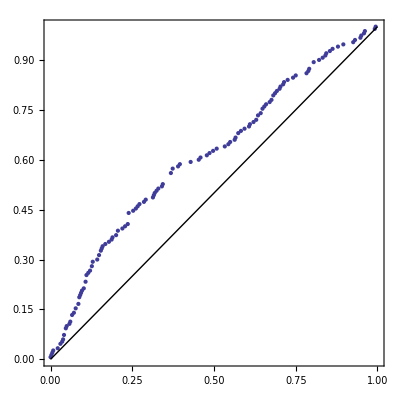

```mathematica
ProbabilityPlot[alleU19[[All,3]],UniformDistribution[{1,365}]]
```

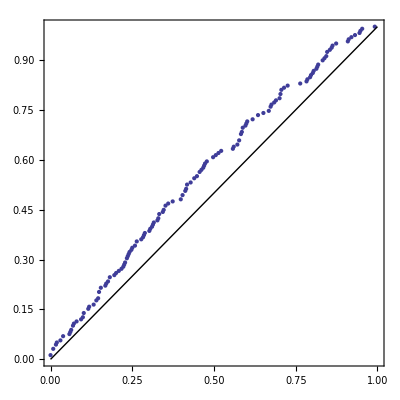

```mathematica
ProbabilityPlot[alleProfis[[All,3]],UniformDistribution[{1,365}]]
```

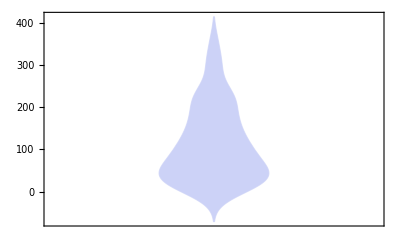

```mathematica
DistributionChart[alleU15[[All,7]]]
```

```mathematica
DensityHistogram[alleU15[[All,7]]]
```

DensityHistogram::ldata: {315, 178, 61, 188, 290, 216, 54, 148, 16, 81, 186, 157, 123, 132, 70, 64, 97, 191, 27, 345, 19, 42, 62, 2, 6, 24, 28, 56, 57, 73, 86, 90, 105, 116, 122, 155, 198, 224, 224, 224, 231, 232, 244, 273, 303, 42, 148, 196, 104, 195, « 93 »} is not a valid dataset or list of datasets.

DensityHistogram[{315,178,61,188,290,216,54,148,16,81,186,157,123,132,70,64,97,191,27,345,19,42,62,2,6,24,28,56,57,73,86,90,105,116,122,155,198,224,224,224,231,232,244,273,303,42,148,196,104,195,282,125,84,151,59,201,130,220,239,27,136,84,175,84,7,98,27,59,33,49,3,14,102,184,360,311,5,51,54,155,191,75,13,10,12,13,14,20,21,24,27,38,39,41,42,42,55,63,94,124,169,183,307,216,147,19,179,89,114,48,78,13,175,120,300,15,99,94,230,137,124,45,123,29,82,108,10,344,148,149,222,134,13,364,41,8,45,71,94,61,31,321,46}]

```mathematica
StringMatchQ[data[[All,1]],"FC B*"];
```

```mathematica
data[[All,7]];
```

```mathematica
alleU15=Select[data,#[[2]]==="U15"&];
```

```mathematica
alleU17=Select[data,#[[2]]==="U17"&];
```

```mathematica
alleU19=Select[data,#[[2]]==="U19"&];
```

```mathematica
alleProfis=Select[data,#[[2]]==="Profis"&];
```

```mathematica
alleU15;
```

```mathematica
KolmogorovSmirnovTest[bayernU15[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

0.0396433

```mathematica
KolmogorovSmirnovTest[alleU15[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

1.78214×10^-11

```mathematica
KolmogorovSmirnovTest[alleU17[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

1.61318×10^-10

```mathematica
KolmogorovSmirnovTest[alleU19[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

8.71197×10^-6

```mathematica
KolmogorovSmirnovTest[alleProfis[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

0.0244386

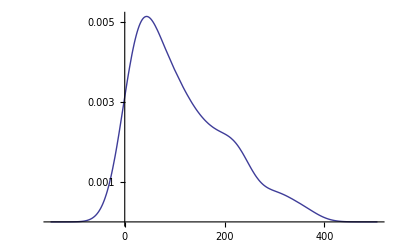

```mathematica
SmoothHistogram[alleU15[[All,7]]]
```

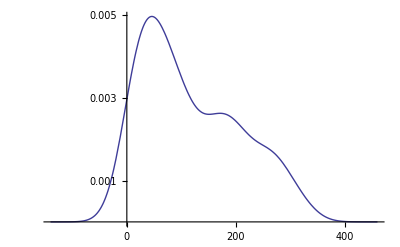

```mathematica
SmoothHistogram[alleU17[[All,7]]]
```

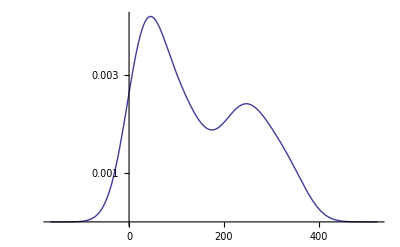

```mathematica
SmoothHistogram[alleU19[[All,7]]]
```

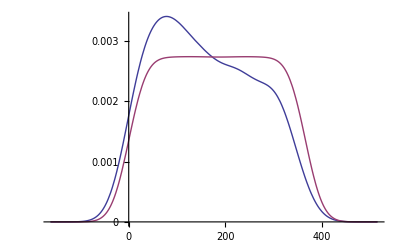

```mathematica
SmoothHistogram[{alleProfis[[All,7]],Range[365]}]
```

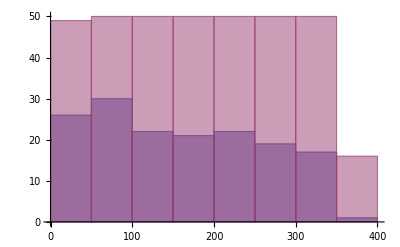

```mathematica
Histogram[{alleProfis[[All,7]],Range[365]}]
```

```mathematica
Length[RandomVariate[UniformDistribution[{181,181}],130]]
```

130

```mathematica
Table[181,{130}]
```

{181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181,181}

```mathematica
Length[alleProfis]
```

130

```mathematica
alleProfis[[All,7]]
```

{86,148,4,219,286,38,250,246,315,121,72,97,23,126,336,175,204,213,4,89,340,257,256,191,12,153,218,129,279,209,314,62,87,127,298,54,173,27,161,67,1,214,105,348,257,95,157,299,52,122,15,8,15,35,43,49,80,83,97,112,120,122,132,137,148,151,152,167,167,169,172,213,291,297,304,309,332,215,164,211,114,57,293,92,116,362,306,24,55,265,346,102,111,226,115,74,161,86,44,312,106,91,309,290,57,182,151,246,185,104,188,182,171,4,26,38,7,232,232,261,215,294,77,247,304,319,238,211,55,37}

```mathematica
?NormalDistribution
```

RowBox[{"NormalDistribution", "[", RowBox[{StyleBox["μ", "TR"], ",", StyleBox["σ", "TR"]}], "]"}] represents a normal (Gaussian) distribution with mean StyleBox["μ", "TR"] and standard deviation StyleBox["σ", "TR"].
RowBox[{"NormalDistribution", "[", "]"}] represents a normal distribution with zero mean and unit standard deviation.

```mathematica
?KolmogorovSmirnovTest
```

KolmogorovSmirnovTest[data] tests whether data is normally distributed using the Kolmogorov–Smirnov test.
KolmogorovSmirnovTest[data,dist] tests whether data is distributed according to dist using the Kolmogorov–Smirnov test.
KolmogorovSmirnovTest[data,dist,property] returns the value of "property".

```mathematica
KolmogorovSmirnovTest[alleU15[[All,7]],UniformDistribution[{1,365}]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the "KolmogorovSmirnov" test, which assumes unique values.

3.38524×10^-11

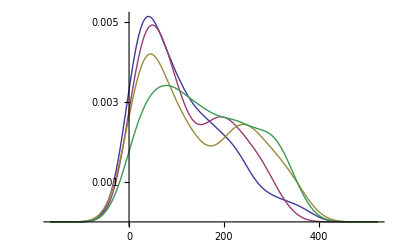

```mathematica
SmoothHistogram[{alleU15[[All,3]],alleU17[[All,3]],alleU19[[All,3]],alleProfis[[All,3]]},Axes->{True,False},PlotRange->Automatic]
```

```mathematica
?UniformDistribution
```

UniformDistribution[{min,max}] represents a continuous uniform statistical distribution giving values between min and max. 
UniformDistribution[] represents a uniform distribution giving values between 0 and 1.
UniformDistribution[{{x_min,x_max},{y_min,y_max},…}] represents a multivariate uniform distribution over the region {{x_min,x_max},{y_min,y_max},…}.

```mathematica
?KolmogorovSmirnovTest
```

KolmogorovSmirnovTest[data] tests whether data is normally distributed using the Kolmogorov–Smirnov test.
KolmogorovSmirnovTest[data,dist] tests whether data is distributed according to dist using the Kolmogorov–Smirnov test.
KolmogorovSmirnovTest[data,dist,property] returns the value of "property".

```mathematica
?RandomVariate
```

RandomVariate[dist] gives a pseudorandom variate from the symbolic distribution dist.
RandomVariate[dist,n] gives a list of n pseudorandom variates from the symbolic distribution dist.
RandomVariate[dist,{n_1,n_2,…}] gives an n_1× n_2×… array of pseudorandom variates from the symbolic distribution dist.

```mathematica
RandomVariate[UniformDistribution[{1,365}]]
```

277.956

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

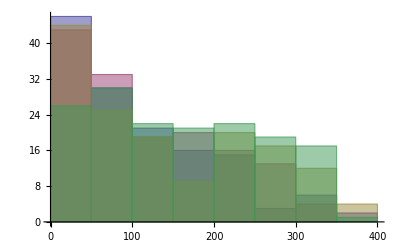

```mathematica
Histogram[{alleU15[[All,7]],alleU17[[All,7]],alleU19[[All,7]],alleProfis[[All,7]]}]
```

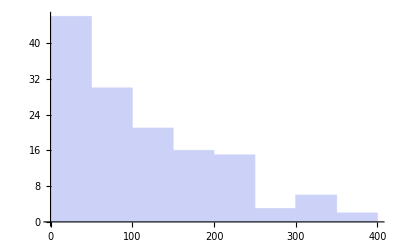

```mathematica
Histogram[alleU15[[All,7]]]
```

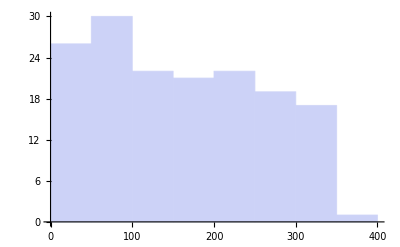

```mathematica
Histogram[alleProfis[[All,7]]]
```

```mathematica
f[x_]=1/365
```

1/365

```mathematica
?Repeat
```

Information::notfound: Symbol "Repeat" not found.

```mathematica
Table[1/365,{20}]
```

{1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365,1/365}

```mathematica
<<MultivariateStatistics`
```

```mathematica
SpearmanRankCorrelation[Range[6],rangu15]
```

-13/(√1190)

```mathematica
rangu15={130,94,40,94,116,54}
```

{130,94,40,94,116,54}

```mathematica
Range[6]
```

{1,2,3,4,5,6}

{{Rang ,Verein ,Liga,Spiele ,S ,U ,N ,Tore ,,,Tordiff. ,Punkte ,Median},{1,VfB Stuttgart,Regio Süd,11, 8  , 2  ,1,38,:,10,28,26,130},{2,FC Bayern München,Regio Süd,11,8, 0  , 3  ,32,:,15,17,24,94},{3,1. FC Nürnberg,Regio Süd,11,7, 0  , 4  ,29,:,17,12,21,40},{4,SC Freiburg,Regio Süd,11,6, 0  , 5  ,23,:,19,4,18,94},{5,Borussia Mönchengladbach,Regio West,11,5,2,4,25,:,16,9,17,116},{6,TSV 1860 München,Bayernliga,11,11,0,0,52,:,6,46,33,54}}

```mathematica
rang2
```

{{Rang ,Verein ,Liga,Gruppe,Median},{2,VfB Stuttgart,Regio Süd,U15,130},{3,FC Bayern München,Regio Süd,U15,94},{4,1. FC Nürnberg,Regio Süd,U15,40},{5,SC Freiburg,Regio Süd,U15,94},{19,TSV 1860 München,Bayernliga,U15,54},{6,Borussia Mönchengladbach,Regio West,U15,116},{1,1. FC Nürnberg,B-Jun. Bundesliga Süd,U17,100},{3,VfB Stuttgart,B-Jun. Bundesliga Süd,U17,75},{4,TSV 1860 München,B-Jun. Bundesliga Süd,U17,117},{5,Bayern München,B-Jun. Bundesliga Süd,U17,101.5},{10,SC Freiburg,B-Jun. Bundesliga Süd,U17,85.5},{4,VfL Borussia Mönchengladbach,B-Jun. Bundesliga West,U17,128},{1,VfB Stuttgart,A-Jun. Bundesliga Süd,U19,141},{2,SC Freiburg,A-Jun. Bundesliga Süd,U19,135},{4,FC Bayern München,A-Jun. Bundesliga Süd,U19,112.5},{5,TSV 1860 München,A-Jun. Bundesliga Süd,U19,112},{8,1. FC Nürnberg,A-Jun. Bundesliga Süd,U19,137},{3,Borussia Mönchengladbach,A-Jun. Bundesliga West,U19,88},{1,FC Bayern München,1. Bundesliga,Profis,183},{4,Borussia Mönchengladbach ,1. Bundesliga,Profis,142.5},{8,VfB Stuttgart ,1. Bundesliga,Profis,115.5},{15,1. FC Nürnberg ,1. Bundesliga,Profis,108.5},{18,SC Freiburg ,1. Bundesliga,Profis,129},{26,TSV 1860 München,2. Bundesliga,Profis,185}}

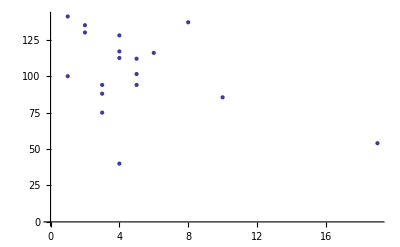

```mathematica
ListPlot[rang3]
```

```mathematica
rang3
```

{{2,130},{3,94},{4,40},{5,94},{19,54},{6,116},{1,100},{3,75},{4,117},{5,101.5},{10,85.5},{4,128},{1,141},{2,135},{4,112.5},{5,112},{8,137},{3,88},{}}

```mathematica
Mean[rang3]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{{2, 130}, {3, 94}, {4, 40}, {5, 94}, {19, 54}, {6, 116}, {1, 100}, {3, 75}, {4, 117}, {5, 101.5}, {10, 85.5}, {4, 128}, {1, 141}, {2, 135}, {4, 112.5}, {5, 112}, {8, 137}, {3, 88}, {""}}].

Mean[{{2,130},{3,94},{4,40},{5,94},{19,54},{6,116},{1,100},{3,75},{4,117},{5,101.5},{10,85.5},{4,128},{1,141},{2,135},{4,112.5},{5,112},{8,137},{3,88},{}}]

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
lm=LinearModelFit[rang3,x,x]
```

FittedModel[117.625-2.88485 x]

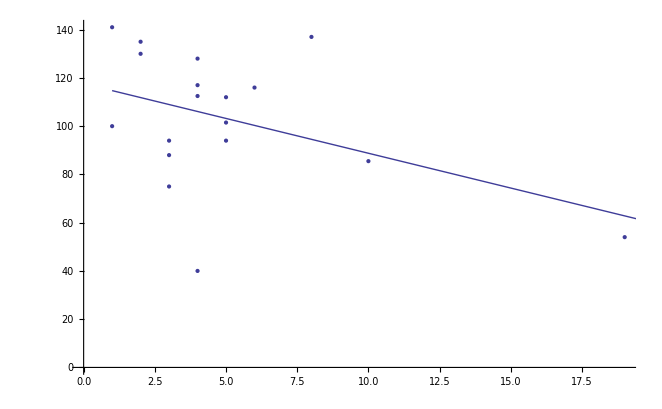

```mathematica
Show[ListPlot[rang3],Plot[lm[x],{x,1,150}]]
```

```mathematica
Correlation[rang3]//MatrixForm
```

(1. | -0.42992
-0.42992 | 1.)

```mathematica
lm2=LinearModelFit[rang4,x,x]
```

FittedModel[141.894+0.168552 x]

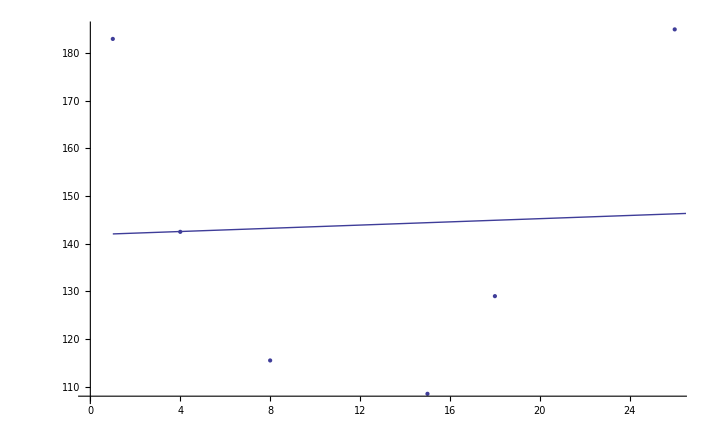

```mathematica
Show[ListPlot[rang4],Plot[lm2[x],{x,1,150}]]
```